Orignal function is: ⅇ^(-x^2)

Approching function is: ⅇ^(-x^2)

Now we begin to use discrete numberical method:

First, let's do some experience about fourier transform.

The length X = 3.716922188849838

delta = 0.8452134572561298

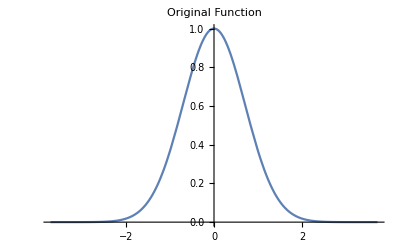

Pi/X = 0.8452134572561298

The needed L is : 7.433844377699677

Actually, L is the product of delta and Nterms = 7.433844377699677

The number of terms we keep for plane wave function = 9

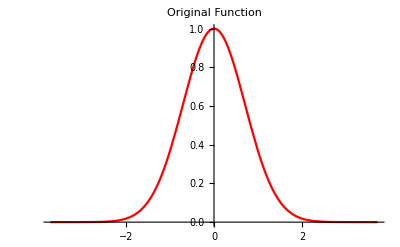

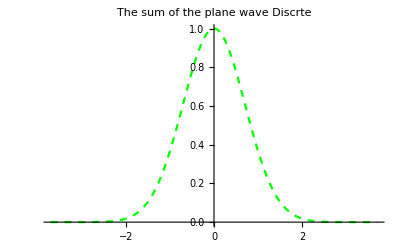

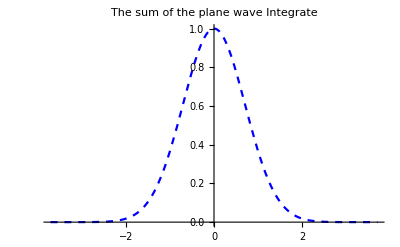

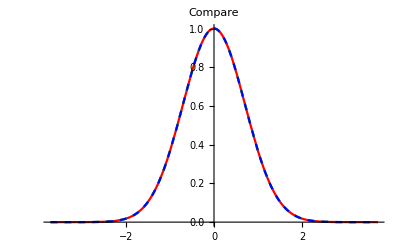

The maximum error between Original function and approximate Integrate function = 0

The maximum error between Integrate function and approximate discrete function = 9.918363177354736×10^-7

The maximum error between Original function and approximate discrete function = 9.918363177354736×10^-7

```mathematica
Clear["Global`*"];
OriFun=Exp[-x^2];
i=Sqrt[-1];
Print["Orignal function is: ",OriFun];
NormCoef=1/(2*Sqrt[Pi]);
L=Infinity;
approchFun=NormCoef*Integrate[Exp[-z^2/4]*Exp[i*z*x],{z,-L,L}];
Print["Approching function is: ",approchFun];
Print["Now we begin to use discrete numberical method: \n"];
Print["First, let's do some experience about fourier transform."];
(*x=2;*)
epsilon=10^-6;
X=Sqrt[-Log[epsilon]];
Print["The length X = ",N[X,16]];
delta=Pi/X;
Print["delta = ",N[delta,16]];
Plot[OriFun,{x,-X,X},PlotLabel->"Original Function"]
sumOfDisFun=0;
sumOfIntFun=0;
Print["Pi/X = ",N[Pi/X,16]];
planeWaveFun[x_]:=NormCoef*Exp[-z^2/4]*Exp[i*z*x]*delta;
(*Plot[Re[NormCoef*Exp[-z^2/4]*Exp[i*z*x]*delta],{x,0,20}]*)
(*Print["planewaveFun = ",planeWaveFun[x]];*)
(*Nterms=30;*)
Print["The needed L is : ",N[Sqrt[-Log[epsilon]*4],16]];
L=Sqrt[-Log[epsilon]*4];
(*L=Nterms*delta;*)
Nterms=Ceiling[L/delta];
Print["Actually, L is the product of delta and Nterms = ",N[L,16]];
Print["The number of terms we keep for plane wave function = ",Nterms];
sumOfIntFun=Re[approchFun];
For[j=-Nterms,j<Nterms+1,j++,
(*Print["\nThe k = ",j];*)
k=j;
z=k*delta;
(*title=Print["The ",j,"th plane wave"];*)
(*Plot[Re[NormCoef*Exp[-z^2/4]*Exp[i*z*x]*delta],{x,-X,X},PlotLabel->title]//Print;*)
(*sumOfFun=sumOfFun+NormCoef*Exp[-z^2/4]*Exp[i*z*x]*delta;*)
sumOfDisFun=sumOfDisFun+Re[planeWaveFun[x]];
(*sumOfIntFun=sumOfIntFun+Re[approchFun];*)
];
p1=Plot[OriFun,{x,-X,X},PlotStyle->Red,PlotLabel->"Original Function"]
(*The following part try to plot the sum of discrete function for different delta. *)
(*For[j=1,j<10,j++,
delta=0.5*j;
sumOfDisFun=0;
For[l=-Nterms,l<Nterms+1,l++,
k=l;
z=k*delta;
sumOfDisFun=sumOfDisFun+Re[planeWaveFun[x]];
];
Print["\nThe delta = ",delta];
p3=Plot[sumOfDisFun,{x,0,20},PlotStyle->{Blue,Dashed},PlotLabel->"The sum of the plane wave Discrte"]//Print
];*)
(*delta=delta/j;*)
p2=Plot[sumOfDisFun,{x,-X,X},PlotStyle->{Green,Dashed},PlotLabel->"The sum of the plane wave Discrte"]
p3=Plot[sumOfIntFun,{x,-X,X},PlotStyle->{Blue,Dashed},PlotLabel->"The sum of the plane wave Integrate"]
Show[p1,p2,p3,PlotLabel->"Compare"]
NumPoints=10000;
f[t_]:=-X+2X/NumPoints*t;
PointTest=Array[f,NumPoints+1,{0,NumPoints}];
ErrorOriToIntResult=Table[0,{Length[PointTest]}];
ErrorIntToDisResult=Table[0,{Length[PointTest]}];
ErrorOriToDisResult=Table[0,{Length[PointTest]}];
For[j=1,j<Length[PointTest]+1,j++,
x=PointTest[[j]];
ErrorOriToIntResult[[j]]=Abs[OriFun-sumOfIntFun];
ErrorIntToDisResult[[j]]=Abs[sumOfIntFun-sumOfDisFun];
ErrorOriToDisResult[[j]]=Abs[OriFun-sumOfDisFun];
];
Print["The maximum error between Original function and approximate Integrate function = ",N[Max[ErrorOriToIntResult],16]];
Print["The maximum error between Integrate function and approximate discrete function = ",N[Max[ErrorIntToDisResult],16]];
Print["The maximum error between Original function and approximate discrete function = ",N[Max[ErrorOriToDisResult],16]];
```